Para el caso del estadio (P(s) vs s)

```mathematica
(*ClearAll["Global`*"];*)

fShape[m_,mR_,nU_]:=Module[{mC=mR/2},If[m<=mC,nU,Floor[Sqrt[Max[0,nU^2-(m-mC)^2]]]]];

StadiumPointsPaper[mR_Integer?NonNegative,nU_Integer?NonNegative]:=Module[{pts={}},Do[With[{nMax=fShape[m,mR,nU]},pts=Join[pts,Table[{m,n},{n,0,nMax}]];],{m,0,mR}];
pts];


BuildWalkMatricesPaper[mR_Integer?NonNegative,nU_Integer?NonNegative]:=Module[{pts,nPos,posToIndex,dim,rulesN={},rulesM={},globalIndex,mMin,mMax,nMin,nMax,m,n,idxU,idxD,target,tIdxU,tIdxD},pts=RandomSample@StadiumPointsPaper[mR,nU];
nPos=Length[pts];
posToIndex=AssociationThread[pts->Range[nPos]];
dim=2 nPos;
mMin=Min[pts[[All,1]]];mMax=Max[pts[[All,1]]];
nMin=Min[pts[[All,2]]];nMax=Max[pts[[All,2]]];
globalIndex[{mm_,nn_},spin_]:=Module[{k=posToIndex[{mm,nn}]},2 (k-1)+If[spin==="U",1,2]];
Do[If[!KeyExistsQ[posToIndex,{m,n}],Continue[]];
idxU=globalIndex[{m,n},"U"];
idxD=globalIndex[{m,n},"D"];
target={m,n+1};
If[KeyExistsQ[posToIndex,target],tIdxU=globalIndex[target,"U"];
AppendTo[rulesN,{tIdxU,idxU}->1],AppendTo[rulesN,{idxD,idxU}->1]];
target={m,n-1};
If[KeyExistsQ[posToIndex,target],tIdxD=globalIndex[target,"D"];
AppendTo[rulesN,{tIdxD,idxD}->1],AppendTo[rulesN,{idxU,idxD}->1]];
(*Wm:horizontal*)target={m+1,n};
If[KeyExistsQ[posToIndex,target],tIdxU=globalIndex[target,"U"];
AppendTo[rulesM,{tIdxU,idxU}->1],AppendTo[rulesM,{idxD,idxU}->1]];
target={m-1,n};
If[KeyExistsQ[posToIndex,target],tIdxD=globalIndex[target,"D"];
AppendTo[rulesM,{tIdxD,idxD}->1],AppendTo[rulesM,{idxU,idxD}->1]];,{m,mMin,mMax},{n,nMin,nMax}];
<|"Points"->pts,"Wn"->SparseArray[rulesN,{dim,dim}],"Wm"->SparseArray[rulesM,{dim,dim}]|>];

CoinD[theta_]:={{Cos[theta],Sin[theta]},{-Exp[I Pi/4] Sin[theta],Exp[I Pi/4] Cos[theta]}};

BuildStepOperatorPaper[mR_Integer?NonNegative,nU_Integer?NonNegative,alpha_,beta_]:=Module[{data,pts,nPos,Wn,Wm,C1,C2,C1Full,C2Full,U},data=BuildWalkMatricesPaper[mR,nU];
pts=data["Points"];
Wn=data["Wn"];
Wm=data["Wm"];
nPos=Length[pts];
C1=CoinD[alpha];
C2=CoinD[beta];C1Full=SparseArray@KroneckerProduct[C1,IdentityMatrix[nPos,SparseArray]];
C2Full=SparseArray@KroneckerProduct[C2,IdentityMatrix[nPos,SparseArray]];
C1Full=SparseArray@KroneckerProduct[IdentityMatrix[nPos,SparseArray],C1];
C2Full=SparseArray@KroneckerProduct[IdentityMatrix[nPos,SparseArray],C2];
U=Wn.C2Full.Wm.C1Full;
SparseArray[U]];


UnitaryErrorFrobeniusMachine[U_]:=Module[{Um},Um=N[U];Norm[ConjugateTranspose[Um].Um-IdentityMatrix[Length[Um]],"Frobenius"]];

ComputeSpacings2PiDenseMachine[U_]:=Module[
{Ud,vals,phases,s},Ud=Normal@N[U];vals=Eigenvalues[Ud];phases=Sort[Mod[Arg[vals],2 Pi]];
s=Differences[Append[phases,First[phases]+2 Pi]];
s/Mean[s]];

PlotPs[sVals_]:=Module[{pPois,pWD,hist,curves},pPois[s_]:=Exp[-s];
pWD[s_]:=(Pi/2) s Exp[-Pi s^2/4];
hist=Histogram[sVals,Automatic,"PDF",ChartStyle->Directive[RGBColor[1,0.8,0],EdgeForm[Black]]];
curves=Plot[{pPois[s],pWD[s]},{s,0,4.5},PlotStyle->{{Thick,Blue},{Thick,Orange}},PlotRange->All];
Show[hist,curves,Frame->True,FrameLabel->{"s","P(s)"}]];
```

```mathematica
Subdivide[0,2Pi,8]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

UnitaryMatrixQ[Ustep] = True

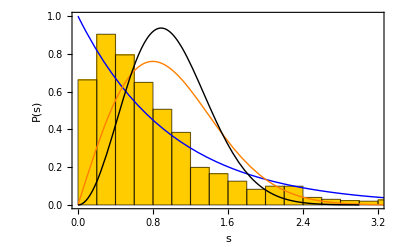

```mathematica
mR=40;
nU=mR/2;
alpha=3Pi/4.;
beta=Pi/4.;
Ustep=BuildStepOperatorPaper[mR,nU,alpha,beta];

Print["UnitaryMatrixQ[Ustep] = ",UnitaryMatrixQ[Ustep]];
sVals=ComputeSpacings2PiDenseMachine[Ustep];
Show[PlotPs[sVals],Plot[PGUE[s],{s,0,3},PlotRange->All,AxesLabel->{"s","P(s)"},PlotStyle->{Thick,Black},GridLines->Automatic,PlotLabel->"Wigner surmise (GUE):  P(s) = (32/π^2) s^2 exp[-(4/π) s^2]"]]
```

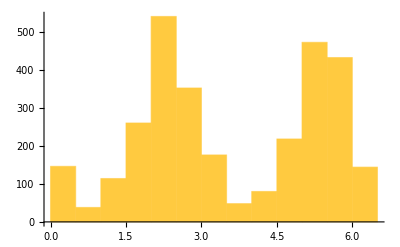

```mathematica
Histogram[Mod[Arg[Eigenvalues[Normal@N@Ustep]],2Pi],Automatic,"Intensity"]
```

```mathematica
PGUE[s_]:=(32/π^2) s^2 Exp[-(4/π) s^2]
```

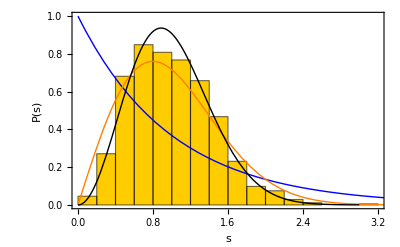

```mathematica
Show[PlotPs[sVals],Plot[PGUE[s],{s,0,3},PlotRange->All,AxesLabel->{"s","P(s)"},PlotStyle->{Thick,Black},GridLines->Automatic,PlotLabel->"Wigner surmise (GUE):  P(s) = (32/π^2) s^2 exp[-(4/π) s^2]"]]
```

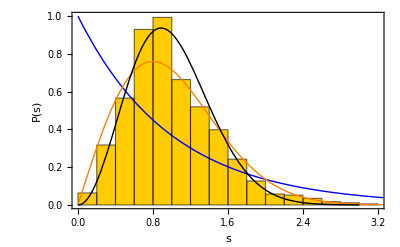

```mathematica
Show[PlotPs[sVals],Plot[PGUE[s],{s,0,3},PlotRange->All,AxesLabel->{"s","P(s)"},PlotStyle->{Thick,Black},GridLines->Automatic,PlotLabel->"Wigner surmise (GUE):  P(s) = (32/π^2) s^2 exp[-(4/π) s^2]"]]
```

Empieza

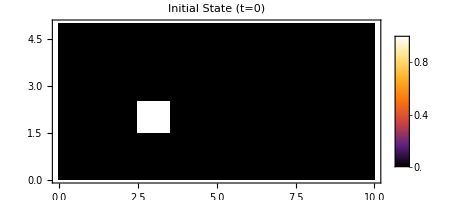

```mathematica
(*Helper to find the index of the center point*)
coords=StadiumPointsPaper[mR,nU];
centerPoint={Floor[(mR/2+nU)/2],Floor[nU/2]}(*Approximate center*);

psi0=Flatten[KroneckerProduct[SparseArray[{21}->1.,56],{1,0} (*Spin Up*)]];

ListDensityPlot[
Flatten/@Transpose[{coords,Partition[Abs[psi0]^2,2][[All,1]]+Partition[Abs[psi0]^2,2][[All,2]]}],
ColorFunction->"SunsetColors",PlotLabel->"Initial State (t=0)",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
(*Number of steps*)
tMax=1;

(*Evolve!*)
(*This applies EvolutionStep repeatedly to psi0*)
trajectory=NestList[Ustep.#&,psi0,tMax];

Print["Simulation complete. Generated ",Length[trajectory]," states."];
```

Simulation complete. Generated 2 states.

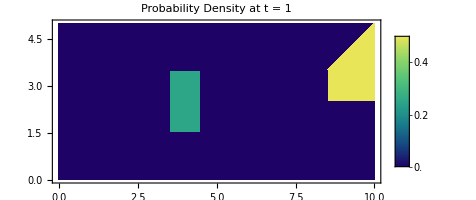

```mathematica
(*Function to convert state vector to plot-able data*)
StateToPlotData[stateVector_,coordinates_]:=Module[
{probs},
(*1. Calculate|amplitude|^2*)
probs=Abs[stateVector]^2;
(*2. Sum Up and Down spin components for each site*)
(*The vector is {Site1_Up,Site1_Down,Site2_Up,Site2_Down...}*)
(*We partition by 2 and sum the sublists*)
probs=Total/@Partition[probs,2];
(*3. Combine with coordinates*)
MapThread[Append,{coordinates,probs}]
];

(*Plot the final state*)
finalPlotData=StateToPlotData[Last[trajectory],coords];

ListDensityPlot[finalPlotData,
ColorFunction->"BlueGreenYellow",PlotLabel->Row[{"Probability Density at t = ",tMax}],PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,ColorFunctionScaling->True]
```

```mathematica
Tuples[{coords,{0,1}}][[110]]
```

{{9,3},1}

```mathematica
Position[trajectory[[2]]//Normal,x_/;x!=0.]
```

{{53},{55},{109},{110}}

```mathematica
ListAnimate[ListDensityPlot[StateToPlotData[#,coords],PlotRange->{{-0.5,2.5},{-0.5,1.5},All},
ColorFunction->"BlueGreenYellow",PlotLabel->Row[{"Probability Density at t = ",tMax}],PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,ColorFunctionScaling->True]&/@trajectory]
```

```mathematica
StateToPlotData[#,coords]&/@trajectory
```

{{{0,0,0},{0,1,0},{1,0,1},{1,1,0},{2,0,0}},{{0,0,0.25},{0,1,0.25},{1,0,0.25},{1,1,0.},{2,0,0.25}},{{0,0,0.125},{0,1,0.25},{1,0,0.426777},{1,1,0.0625},{2,0,0.135723}}}

```mathematica
StateToPlotData[psi0,coords]
```

{{0,0,0},{0,1,0},{1,0,1},{1,1,0},{2,0,0}}

Fin

Para el rectángulo (P(s) vs s)

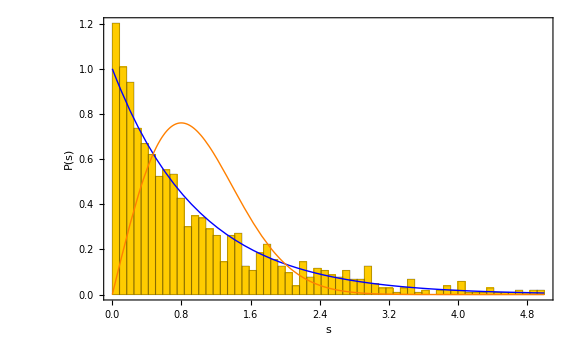

```mathematica
L = 50; A = 25; (*rectángulo*)
alpha = Pi/4.; beta = Pi/3.; (*ángulos del operador moneda*)
esp = 60; showPlotRange = 5; 
posIndex[l_,a_]:=(a-1)*L+l;
globalIndex[l_,a_,spin_]:=2*(posIndex[l,a]-1)+If[spin=="U",1,2];
Ccoin[θ_]:={{Cos[θ],Sin[θ]},{-Exp[I*Pi/4] Sin[θ],Exp[I*Pi/4] Cos[θ]}};
C1=Ccoin[alpha];
C2=Ccoin[beta];
Npos=L*A;dim=2*Npos; (*No de posiciones y dim del espacio de Hilbert*)
Ipos=IdentityMatrix[Npos,SparseArray]; 

lVals=Flatten@Table[l,{a,1,A},{l,1,L}];
aVals=Flatten@Table[a,{a,1,A},{l,1,L}];(*Identidad*)
Uidx=globalIndex@@@Transpose[{lVals,aVals,ConstantArray["U",Length[lVals]]}];
Didx=globalIndex@@@Transpose[{lVals,aVals,ConstantArray["D",Length[lVals]]}];
targetU=MapThread[If[#1<L,globalIndex[#1+1,#2,"U"],globalIndex[L,#2,"D"]]&,{lVals,aVals}]; (*devulve el indice de la posicion (l + 1, a) con espin U, es decir mueve a la derecha manteniendo el espin*)
targetD=MapThread[If[#1>1,globalIndex[#1-1,#2,"D"],globalIndex[1,#2,"U"]]&,{lVals,aVals}];
rWm=Join[MapThread[{#1,#2}->1&,{targetU,Uidx}],MapThread[{#1,#2}->1&,{targetD,Didx}]]; (*resolver errores dimensionales*)

Wm=SparseArray[rWm,{dim,dim}];
targetU2=MapThread[If[#2<A,globalIndex[#1,#2+1,"U"],globalIndex[#1,A,"D"]]&,{lVals,aVals}];
targetD2=MapThread[If[#2>1,globalIndex[#1,#2-1,"D"],globalIndex[#1,1,"U"]]&,{lVals,aVals}];

rWn=Join[MapThread[{#1,#2}->1&,{targetU2,Uidx}],MapThread[{#1,#2}->1&,{targetD2,Didx}]];

Wn=SparseArray[rWn,{dim,dim}];
C1t=KroneckerProduct[C1,Ipos];
C2t=KroneckerProduct[C2,Ipos];
Qw=Wn.C2t.Wm.C1t;  (*libro*)
eigvals=Eigenvalues[Normal[Qw]];
eigvals=Eigenvalues[Normal[Qw]];

phases=Sort[Mod[Arg[eigvals],2 Pi]];

(*Cerrar el círculo:N espaciamientos,no N-1*)
Es=Differences[Append[phases,First[phases]+2 Pi]];

sUnfold=Es/Mean[Es];

poisson[s_]:=Exp[-s];
wigner[s_]:=(Pi/2) s Exp[-Pi s^2/4];

hist=Histogram[sUnfold,{0,showPlotRange,showPlotRange/esp},"ProbabilityDensity",ChartStyle->Directive[RGBColor[1,0.8,0],EdgeForm[Black]]];

curves=Plot[{poisson[s],wigner[s]},{s,0,showPlotRange},PlotStyle->{{Thick,Blue},{Thick,Orange}},PlotRange->All];

Show[hist,curves,Frame->True,FrameLabel->{"s","P(s)"},PlotRange->{{0,showPlotRange},{0,All}},ImageSize->Large]
```

Pureza estadio

```mathematica
dim=Length[Ustep];
nPos=dim/2;
k0=Ceiling[nPos/2];

psi0=ConstantArray[0.,dim];
psi0[[2 (k0-1)+1]]=1/Sqrt[2];   
psi0[[2 (k0-1)+2]]=I/Sqrt[2];   
psi0=psi0/Norm[psi0];
tSteps=10;  

Ud=Normal@N[Ustep];                 
psiT=MatrixPower[Ud,tSteps].psi0;
psiT=psiT/Norm[psiT];

rho=Outer[Times,psiT,Conjugate[psiT]];  (*densidad total*)

resh=ArrayReshape[rho,{nPos,2,nPos,2}];

rhoCoin=Table[Sum[resh[[k,a,k,b]],{k,1,nPos}],{a,1,2},{b,1,2}]//Chop;

purityCoin=Tr[rhoCoin.rhoCoin]//Chop;

Print["Pureza= ",purityCoin];
```

Pureza= 0.517886

Pureza moneda rectángulo

```mathematica
dim=Length[Qw];
nPos=dim/2;
k0=Ceiling[nPos/2];
psi0=ConstantArray[0.,dim];
psi0[[2 (k0-1)+1]]=1/Sqrt[2];   
psi0[[2 (k0-1)+2]]=I/Sqrt[2];   
psi0=psi0/Norm[psi0];

tSteps=10; 

Ud=Normal@N[Qw];                  
psiT=MatrixPower[Ud,tSteps].psi0;
psiT=psiT/Norm[psiT];
rho=Outer[Times,psiT,Conjugate[psiT]];
resh=ArrayReshape[rho,{nPos,2,nPos,2}];
rhoCoin=Table[Sum[resh[[k,a,k,b]],{k,1,nPos}],{a,1,2},{b,1,2}]//Chop;

purityCoin=Tr[rhoCoin.rhoCoin]//Chop;
Print["Pureza = ",purityCoin];
```

Pureza = 0.625

Gráfica Pureza estadio - rectángulo

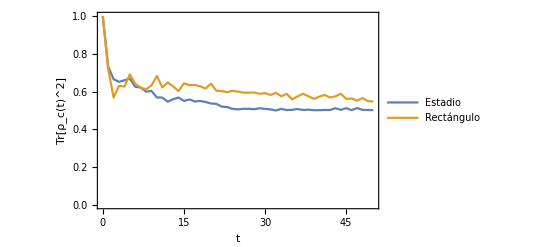

```mathematica
PurityVsTimeFromU[U_,coin0_List,tMax_Integer]:=Module[{dim,nPos,posUniform,psi0Uniform,Ud,rhoCoinFromPsi,purityFromPsi},dim=Length[U];
nPos=dim/2;
posUniform=ConstantArray[1/Sqrt[nPos],nPos];
psi0Uniform=Flatten@KroneckerProduct[posUniform,coin0/Norm[coin0]];
psi0Uniform=psi0Uniform/Norm[psi0Uniform];
Ud=Normal@N[U];
rhoCoinFromPsi[psi_]:=Module[{A},A=ArrayReshape[psi,{nPos,2}];
ConjugateTranspose[A].A//Chop];
purityFromPsi[psi_]:=Module[{r=rhoCoinFromPsi[psi]},Tr[r.r]//Chop];
Table[Module[{psiT},psiT=MatrixPower[Ud,t].psi0Uniform;
psiT=psiT/Norm[psiT];
{t,purityFromPsi[psiT]}],{t,0,tMax}]];
coin0={1,I}/Sqrt[2];
tMax=50;
purityStadium=PurityVsTimeFromU[Ustep,coin0,tMax];
RectanglePoints[mR_,nU_]:=Flatten[Table[{m,n},{m,0,mR},{n,0,nU}],1];

BuildWalkMatricesRectangle[mR_,nU_]:=Module[{pts,nPos,posToIndex,dim,rulesN={},rulesM={},globalIndex,m,n,idxU,idxD,target,tIdxU,tIdxD},pts=RectanglePoints[mR,nU];
nPos=Length[pts];
posToIndex=AssociationThread[pts->Range[nPos]];
dim=2 nPos;
globalIndex[{mm_,nn_},spin_]:=Module[{k=posToIndex[{mm,nn}]},2 (k-1)+If[spin==="U",1,2]];
Do[idxU=globalIndex[{m,n},"U"];
idxD=globalIndex[{m,n},"D"];
(*Wn:vertical*)target={m,n+1};
If[KeyExistsQ[posToIndex,target],tIdxU=globalIndex[target,"U"];
AppendTo[rulesN,{tIdxU,idxU}->1],AppendTo[rulesN,{idxD,idxU}->1]];
target={m,n-1};
If[KeyExistsQ[posToIndex,target],tIdxD=globalIndex[target,"D"];
AppendTo[rulesN,{tIdxD,idxD}->1],AppendTo[rulesN,{idxU,idxD}->1]];
(*Wm:horizontal*)target={m+1,n};
If[KeyExistsQ[posToIndex,target],tIdxU=globalIndex[target,"U"];
AppendTo[rulesM,{tIdxU,idxU}->1],AppendTo[rulesM,{idxD,idxU}->1]];
target={m-1,n};
If[KeyExistsQ[posToIndex,target],tIdxD=globalIndex[target,"D"];
AppendTo[rulesM,{tIdxD,idxD}->1],AppendTo[rulesM,{idxU,idxD}->1]];,{m,0,mR},{n,0,nU}];
<|"Points"->pts,"Wn"->SparseArray[rulesN,{dim,dim}],"Wm"->SparseArray[rulesM,{dim,dim}]|>];

Coin[theta_]:={{Cos[theta],Sin[theta]},{-Exp[I Pi/4] Sin[theta],Exp[I Pi/4] Cos[theta]}};

BuildStepOperatorRectangle[mR_,nU_,alpha_,beta_]:=Module[{data,nPos,Wn,Wm,C1Full,C2Full,U},data=BuildWalkMatricesRectangle[mR,nU];
nPos=Length[data["Points"]];
Wn=data["Wn"];Wm=data["Wm"];
C1Full=SparseArray@KroneckerProduct[Coin[alpha],IdentityMatrix[nPos,SparseArray]];
C2Full=SparseArray@KroneckerProduct[Coin[beta],IdentityMatrix[nPos,SparseArray]];
U=Wn.C2Full.Wm.C1Full;
SparseArray[U]];

Urect=BuildStepOperatorRectangle[mR,nU,alpha,beta];
purityRect=PurityVsTimeFromU[Urect,coin0,tMax];

ListLinePlot[{purityStadium,purityRect},Frame->True,FrameLabel->{"t","Tr[ρ_c(t)^2]"},PlotRange->{0,1},PlotLegends->{"Estadio","Rectángulo"}]
```